```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

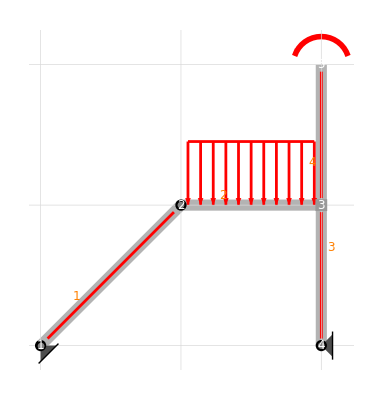

```mathematica
example={$$nodes->{{-L, -L}, {0, 0}, {L, 0}, {L, -L}, {L, L}},
$$edges->{{1, 2}, {2, 3}, {3, 4}, {3, 5}},$$absname->s,
$$constraints->{{{"hinge", 1}}, {{"hinge", 1, 2}}, {{"clamp", 2, 3}, {"clamp", 3, 4}}, {{"hinge", 3}}, {{"free", 4}}},
$$bodyloads->{{2, {0, -q, 0}}},
$$nodalloads->{{5, {0, 0, q L^2}}},
$$predeformations->{{1, {0, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
(*BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];*)
gsol=BFShowOutput[example, sol]
```

BFClassify::sd: Statically determined system.

BFClassify::kd: Kinematically determined system.

123

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Dimensionless abscissa

s

Static equilibrium matrix

{{-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,√2 L,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-√2,√2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-√2,-√2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}

Static equilibrium vector

{0,0,0,0,L q,(L^2 q)/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-L^2 q}

Fredholm condition: are the loads orthogonal to allowed rigid motions?

True

Degree of static undetermination

0

Reactions

{{-(3 L q)/(2 √2),0,0,-(3 L q)/(2 √2),0,0},{-(3 L q)/4,-(3 L q)/4,0,-(3 L q)/4,(L q)/4,(L^2 q)/4},{-(L q)/4,-(3 L q)/4,-(3 L^2 q)/4,-(L q)/4,-(3 L q)/4,0},{0,0,L^2 q,0,0,L^2 q}}

Internal actions (N,Q,M)

{{-(3 L q)/(2 √2),-(3 L q)/4,-(L q)/4,0},{0,-(3 L q)/4+L q s,-(3 L q)/4,0},{0,1/6 L s ((9 L q)/2-3 L q s),1/6 (-(9 L^2 q)/2+9/2 L^2 q s),L^2 q}}

-Graphics-

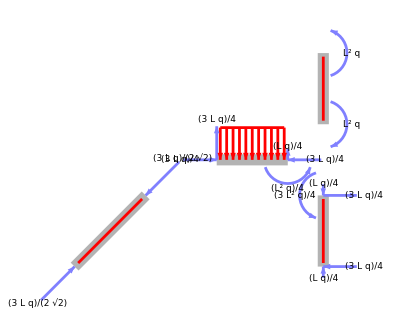

-Graphics-

-Graphics-

-Graphics-